# MathIOmica: Dynamic Transcriptome

Loading the MathIOmica Packagepaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#2133290847 | Classification, Clustering  and Visualization of Transcriptome Time Seriespaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#834625544
Importing OmicsObject Transcriptome Datapaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#257268298 | Annotation and Enrichmentpaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#2035743524
Processing OmicsObject Transcriptome Datapaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#208227830 | Appendix: All Commands Up to Enrichment Analysis in One Steppaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#981111770
Resampling Transcriptome Datapaclet:MathIOmica/tutorial/MathIOmicaDynamicTranscriptome#1956292219 |

The MathIOmica Dynamic Transcriptome is a brief guide to analyzing the dynamics of transcriptome data. The presentation is streamlined, without discussion of the functions used, but with links to each function provided at each step of the calculation. For more details consult MathIOmica's documentation of each funciton, and the MathIOmica Tutorial for a deeper presentation of a multiple omics analysis.

## Loading the MathIOmica Package

The functions defined in the MathIOmica` context provide support for conducting analyses of omics data (See also the MathIOmica Overview).

This loads the package:

```mathematica
<<MathIOmica`
```

## Importing OmicsObject Transcriptome Data

We first import the transcriptomics data example (for details on how to import such data please refer to DataImporterpaclet:MathIOmica/ref/DataImporter, DataImporterDirectpaclet:MathIOmica/ref/DataImporterDirect, DataImporterDirectLabeledpaclet:MathIOmica/ref/DataImporterDirectLabeled and OmicsObjectCreatorpaclet:MathIOmica/ref/OmicsObjectCreator documentation).

We import the transcriptomics OmicsObject

```mathematica
rnaExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"rnaExample"}]]
```

<|7→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{2.73998},{OK}},25262,{LOC100507412,RNA}→{{0},{OK}},{RNA45S5,RNA}→{{0},{OK}},{DUX4L,RNA}→{{0},{OK}}|>,8→<|1|>,11,20→1,21→<|1|>|>
 |  |  |  |

There are multiple samples given by the outer associations. We can use Query to get any data. For example we can get the outer keys:

```mathematica
Query[Keys]@rnaExample
```

{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

We form an association between samples to actual days of the study:

```mathematica
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
```

We can now do a KeyMap to rename the outer keys:

```mathematica
rnaLongitudinal=KeyMap[sampleToDays,rnaExample]
```

<|186→<|{FAM138A,RNA}→{{0},{OK}},{OR4F5,RNA}→{{0},{OK}},{LOC729737,RNA}→{{2.73998},{OK}},25262,{LOC100507412,RNA}→{{0},{OK}},{RNA45S5,RNA}→{{0},{OK}},{DUX4L,RNA}→{{0},{OK}}|>,255→<|1|>,11,380→1,400→<|1|>|>
 |  |  |  |

## Processing OmicsObject Transcriptome Data

We normalize the transcriptome data using the QuantileNormalizationpaclet:MathIOmica/ref/QuantileNormalization function.

```mathematica
rnaQuantileNormed=QuantileNormalization[rnaLongitudinal,ListIndex-> 1,ComponentIndex-> 1]
```

<|186→<|{FAM138A,RNA}→{{0.},{OK}},{OR4F5,RNA}→{{0.},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25262,{LOC100507412,RNA}→{{0.},{OK}},{RNA45S5,RNA}→{{0.},{OK}},{DUX4L,RNA}→{{0.},{OK}}|>,13,400→<|1|>|>
 |  |  |  |

We first use  LowValueTagpaclet:MathIOmica/ref/LowValueTag to tag values of 0 as Missing[]:

```mathematica
rnaZeroTagged=LowValueTag[rnaQuantileNormed,0]
```

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

We next use  LowValueTagpaclet:MathIOmica/ref/LowValueTag again to set all FPKM values <1 to unity:

```mathematica
rnaNoiseAdjusted=LowValueTag[rnaZeroTagged,1,ValueReplacement-> 1]
```

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

We filter out data  using FilterMissingpaclet:MathIOmica/ref/FilterMissing where the reference healthy point "255" is missing and retain data with at least 3/4 points available:

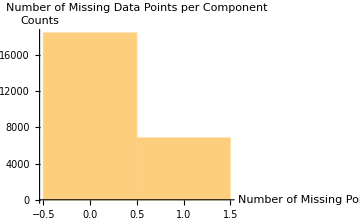

{Missing -> Counts: ,<|0→18427,1→6841|>}

-Graphics-

<|186→<|{FAM138A,RNA}→{{Missing[]},{OK}},{OR4F5,RNA}→{{Missing[]},{OK}},{LOC729737,RNA}→{{2.2946},{OK}},25263,{RNA45S5,RNA}→{{Missing[]},{OK}},{DUX4L,RNA}→{{Missing[]},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

```mathematica
rnaFiltered=FilterMissing[rnaNoiseAdjusted,3/4,Reference-> "255"]
```

We extract the times for the filtered RNA data using TimeExtractorpaclet:MathIOmica/ref/TimeExtractor:

```mathematica
timesRNA=TimeExtractor[rnaFiltered]
```

{186,255,289,290,292,294,297,301,307,311,322,329,369,380,400}

For each gene we now extract a time series (list of values) corresponding to these times using CreateTimeSeriespaclet:MathIOmica/ref/CreateTimeSeries:

```mathematica
timeSeriesRNA=CreateTimeSeries[rnaFiltered]
```

<|{FAM138A,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{OR4F5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{LOC729737,RNA}→{2.2946,1,4.67694,4.48131,4.95507,1,1.25726,2.14767,1.93219,1,2.58217,2.31301,4.10284,3.80929,1.45471},{DDX11L1,RNA}→{5.91665,4.32081,3.19599,3.64164,2.7327,2.13461,2.17168,3.23429,1.89576,3.0267,4.34004,7.27001,2.01132,9.27701,7.54415},25260,{RNA5-8S5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{LOC100507412,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{RNA45S5,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1},{DUX4L,RNA}→{Missing[],1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>
 |  |  |  |

We use SeriesApplierpaclet:MathIOmica/ref/SeriesApplier to implement a logarithm transformation:

```mathematica
timeSeriesRNALog=SeriesApplier[Log,timeSeriesRNA]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.830556,0,1.54264,1.49992,1.60041,0,0.228935,0.764385,0.658653,0,0.94863,0.838548,1.41168,1.33744,0.374807},{DDX11L1,RNA}→{1.77777,1.46344,1.1619,1.29243,1.00529,0.758282,0.775501,1.17381,0.639619,1.10747,1.46788,1.98376,0.698792,2.22754,2.02077},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

We compare every value in each series to the healthy "255" time point, which is the second element in each series. We use SeriesInternalComparepaclet:MathIOmica/ref/SeriesInternalCompare:

```mathematica
rnaCompared=SeriesInternalCompare[timeSeriesRNALog,ComparisonIndex->2]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.830556,0,1.54264,1.49992,1.60041,0,0.228935,0.764385,0.658653,0,0.94863,0.838548,1.41168,1.33744,0.374807},{DDX11L1,RNA}→{0.314326,0.,-0.301545,-0.171011,-0.458154,-0.705162,-0.687943,-0.289634,-0.823824,-0.35597,0.00444068,0.520314,-0.764652,0.764095,0.557328},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

Next, we normalize each series, using again SeriesApplierpaclet:MathIOmica/ref/SeriesApplier:

```mathematica
normedRNACompared=SeriesApplier[Normalize,rnaCompared]
```

<|{FAM138A,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{OR4F5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC729737,RNA}→{0.218293,0.,0.40545,0.39422,0.420632,0.,0.0601705,0.200902,0.173112,0.,0.249326,0.220394,0.371029,0.351517,0.0985097},{DDX11L1,RNA}→{0.156411,0.,-0.150051,-0.0850959,-0.22798,-0.350893,-0.342324,-0.144124,-0.40994,-0.177133,0.00220971,0.258911,-0.380495,0.380218,0.27733},25260,{RNA5-8S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{LOC100507412,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{RNA45S5,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0},{DUX4L,RNA}→{Missing[],0,0,0,0,0,0,0,0,0,0,0,0,0,0}|>
 |  |  |  |

Finally, we use ConstantSeriesCleanpaclet:MathIOmica/ref/ConstantSeriesClean to remove constant series, as we are interested in changing time patterns:

```mathematica
rnaFinalTimeSeries=ConstantSeriesClean[normedRNACompared]
```

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

<|{LOC729737,RNA}→{0.218293,0.,0.40545,0.39422,0.420632,0.,0.0601705,0.200902,0.173112,0.,0.249326,0.220394,0.371029,0.351517,0.0985097},11782,{UTY,RNA}→{-0.0324671,0.,-0.0127666,-0.256982,-0.0805343,-0.152071,3,-0.198929,-0.280753,-0.310545,-0.339742,-0.346361,-0.542312}|>
 |  |  |  |

## Resampling Transcriptome Data

In addition to the above, we want to create a resampled distribution for the transcriptome dataset prior to classification and clustering.  We repeat the steps in the processing section above using a resampled set of measurements.

We create a resampling of 100000 sets using  BootstrapGeneralpaclet:MathIOmica/ref/BootstrapGeneral:

```mathematica
rnaBootstrap=BootstrapGeneral[rnaLongitudinal,100000]
```

<|186→<|1→{{0},{OK}},2→{{0},{OK}},3→{{10.0429},{OK}},4→{{12.8612},{OK}},5→{{2.37963},{OK}},99991,99997→{{43.8242},{OK}},99998→{{2.40797},{OK}},99999→{{4.68299},{OK}},100000→{{3.29531},{OK}}|>,255→<|1|>,11,1,400→<|1|>|>
 |  |  |  |

As with the regular data we: 1. normalize , 2. tag zero values, 3. tag values of FPKM <1, 4. filter missing data, 5. create a time series, 6. take a logarithm, 7. compare to "255" reference, 8. take the norm of each time series, 9. clean out constant series

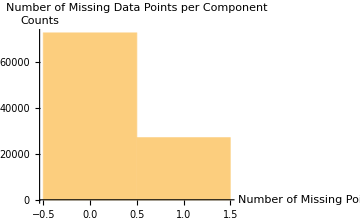

{Missing -> Counts: ,<|0→72867,1→27133|>}

-Graphics-

Removed series and returning filtered list. If you would like a list of removed keys run the command ConstantSeriesClean[data,ReturnDropped → True].

```mathematica
(*1*)rnaBootstrapQuantileNormed=QuantileNormalization[rnaBootstrap,ListIndex-> 1,ComponentIndex-> 1];
(*2*)rnaBootstrapZeroTagged=LowValueTag[rnaBootstrapQuantileNormed,0];
(*3*) rnaBootstrapNoiseAdjusted=LowValueTag[rnaBootstrapZeroTagged,1,ValueReplacement-> 1];
(*4*) rnaBootstrapFiltered=FilterMissing[rnaBootstrapNoiseAdjusted,3/4,Reference-> "255"];
(*5*) timeSeriesBootstrapRNA=CreateTimeSeries[rnaBootstrapFiltered];
(*6*) timeSeriesBootstrapRNALog=SeriesApplier[Log,timeSeriesBootstrapRNA];
(*7*)rnaBootstrapCompared=SeriesInternalCompare[timeSeriesBootstrapRNALog,ComparisonIndex->2];
(*8*)normedBootstrapRNACompared=SeriesApplier[Normalize,rnaBootstrapCompared];
(*9*)rnaBootstrapFinalTimeSeries=ConstantSeriesClean[normedBootstrapRNACompared];
```

## Classification, Clustering and Visualization of Transcriptome Time Series

In this section we will classify the transcriptome time series based on patterns in the series. For the classification we will use TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification.

Before we classify our transcriptome data, we estimate for the "LombScargle" Method a 0.95 quantile cutoff from the bootstrap transcriptome data using QuantileEstimatorpaclet:MathIOmica/ref/QuantileEstimator:

```mathematica
q95RNA=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA]
```

0.85987

Next, we estimate the "Spikes" 0.95 quantile cutoff from the bootstrap transcriptome data:

```mathematica
q95RNASpikes=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA,Method-> "Spikes"]
```

<|14→{0.886757,-0.348387},15→{0.861302,-0.337344}|>

Now we can classify the transcriptome time series data based on these cutoffs using TimeSeriesClassificationpaclet:MathIOmica/ref/TimeSeriesClassification:

```mathematica
rnaClassification=TimeSeriesClassification[rnaFinalTimeSeries,timesRNA,LombScargleCutoff-> q95RNA,SpikeCutoffs->q95RNASpikes]
```

Method → "LombScargle"

<|SpikeMax→<|1|>,7,f7→<|{MIR6723,RNA}→{{0.214503,0.000338299,0.0390479,0.0653206,0.291434,0.336712,0.865961},{1}},60,{DNASE1L1,RNA}→1|>|>
 |  |  |  |

To obtain the possible frequencies we simply run LombScarglepaclet:MathIOmica/ref/LombScargle over the desired times for one of the time series and set the FrequenciesOnly option to Truepaclet:ref/True:

```mathematica
LombScargle[rnaFinalTimeSeries[[1]],timesRNA,FrequenciesOnly-> True]
```

<|f1→0.00500668,f2→0.0104306,f3→0.0158545,f4→0.0212784,f5→0.0267023,f6→0.0321262,f7→0.0375501|>

We now cluster our RNA data using TimeSeriesClusterspaclet:MathIOmica/ref/TimeSeriesClusters:

Agglomerate::ties: 426 ties have been detected; reordering input may produce a different result.

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

General::stop: Further output of Agglomerate::ties will be suppressed during this calculation.

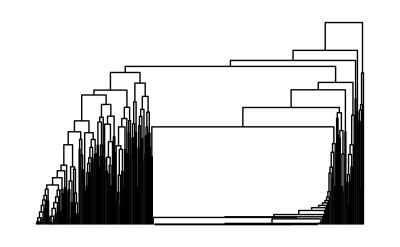
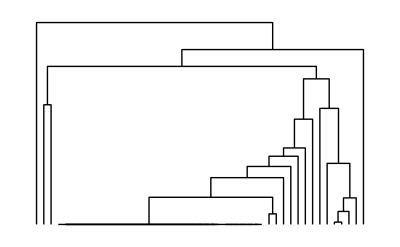
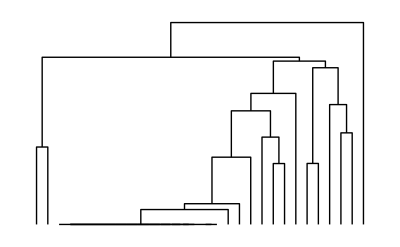
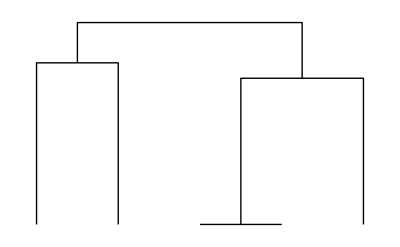
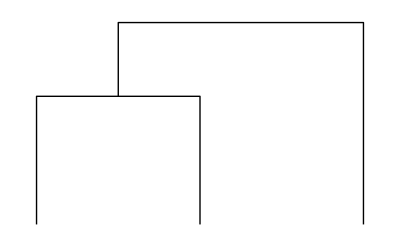
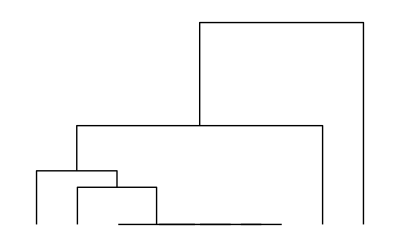
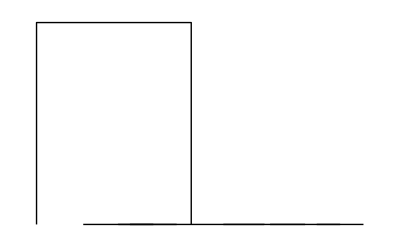
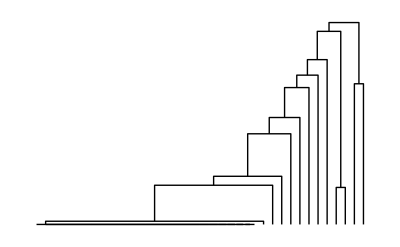
<|SpikeMax→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-,{G1S3}→-Graphics-,{G1S4}→-Graphics-,{G1S5}→-Graphics-,{G1S6}→-Graphics-,{G1S7}→-Graphics-,{G1S8}→-Graphics-,{G1S9}→-Graphics-,{G1S10}→-Graphics-,{G1S11}→-Graphics-,{G1S12}→-Graphics-,{G1S13}→-Graphics-,{G1S14}→-Graphics-|>|>,SpikeMin→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-,{G1S3}→-Graphics-|>|>,f1→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>|>,f2→<|G1→<|{G1S1}→-Graphics-|>,G2→<|{G2S1}→{{0.283264,0.,0.149932,0.415971,0.146512,0.2947,0.267954,0.15466,0.432236,0.281295,0.151677,0.170078,0.149432,0.249221,0.343349}→{POMP,RNA}}|>|>,f3→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>,G2→<|{G2S1}→{{-0.0325957,0.,0.295712,0.400274,0.29765,0.246613,0.0892792,0.27966,0.493911,0.0203708,0.100827,0.223014,0.386987,0.111948,0.221638}→{DUSP23,RNA}},{G2S2}→-Graphics-|>,G3→<|{G3S1}→-Graphics-,{G3S2}→{{-0.0555808,0.,0.317043,0.41872,0.395921,0.283783,0.184223,0.30154,0.265713,0.167588,0.138036,0.110511,0.434502,0.0277974,0.198492}→{PYCARD,RNA}}|>,G4→<|{G4S1}→-Graphics-,{G4S2}→{{0.0572204,0.,-0.22398,-0.11871,-0.0686182,-0.0820599,-0.216559,-0.187636,-0.682766,0.0415532,-0.197678,0.14124,-0.497177,-0.0370276,0.251877}→{ST7,RNA}}|>|>,f4→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>,G2→<|{G2S1}→-Graphics-,{G2S2}→-Graphics-|>|>,f5→<|G1→<|{G1S1}→{{-0.335157,0.,0.107286,0.337104,-0.0121183,0.243878,0.043649,-0.0358548,0.410512,0.305297,0.354136,0.00802356,0.0854209,0.461454,0.303753}→{ALG14,RNA}},{G1S2}→-Graphics-,{G1S3}→-Graphics-|>,G2→<|{G2S1}→-Graphics-,{G2S2}→-Graphics-,{G2S3}→-Graphics-|>|>,f6→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>,G2→<|{G2S1}→-Graphics-,{G2S2}→-Graphics-|>|>,f7→<|G1→<|{G1S1}→-Graphics-,{G1S2}→-Graphics-|>,G2→<|{G2S1}→-Graphics-,{G2S2}→-Graphics-,{G2S3}→-Graphics-|>|>|>

<|1|>
 |  |  |  |

```mathematica
rnaClusters=TimeSeriesClusters[rnaClassification, PrintDendrograms-> True]
```

For each class we can generate a dendrogram/heatmap plot using TimeSeriesDendrogramsHeatmapspaclet:MathIOmica/ref/TimeSeriesDendrogramsHeatmaps, with groupings represented on the left, and highlighted to represent the grouping level. The G, S, columns represent the groupings and subgroupings generated by the clustering.  The legend shows the corresponding groupings and subgrouping, and the number of elements in each group subgroup.

```mathematica
TimeSeriesDendrogramsHeatmaps[rnaClusters]
```

-Graphics-

## Annotation and Enrichment

We can carry out Gene Ontology analysis using GOAnalysispaclet:MathIOmica/ref/GOAnalysis for all the classes and groups/subgroups. We only report terms for which there are at least 3 members (2 sets of GO terms, one each for proteomics and transcriptomics).  Please note that this may be a time consuming computation.

```mathematica
goAnalysisRNA=GOAnalysis[rnaClusters,OntologyLengthFilter-> 3,ReportFilter-> 3 ];
```

The output of GOAnalysispaclet:MathIOmica/ref/GOAnalysis has enrichments for each class and group

```mathematica
Query[Keys]@goAnalysisRNA
```

{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7}

```mathematica
Query[All,Keys]@goAnalysisRNA
```

<|SpikeMax→{G1S1,G1S2,G1S3,G1S4,G1S5,G1S6,G1S7,G1S8,G1S9,G1S10,G1S11,G1S12,G1S13,G1S14},SpikeMin→{G1S1,G1S2,G1S3},f1→{G1S1,G1S2},f2→{G1S1,G2S1},f3→{G1S1,G1S2,G2S1,G2S2,G3S1,G3S2,G4S1,G4S2},f4→{G1S1,G1S2,G2S1,G2S2},f5→{G1S1,G1S2,G1S3,G2S1,G2S2,G2S3},f6→{G1S1,G1S2,G2S1,G2S2},f7→{G1S1,G1S2,G2S1,G2S2,G2S3}|>

We can view results for any of the groups (and also check out the behavior using the heatmaps generated in the previous section

```mathematica
Query["SpikeMax","G1S1"]@goAnalysisRNA
```

<|GO:0005814→{{0.0000103087,0.0133394,True},{193,141,19772,9},{{centriole,cellular_component},{{{AHI1,RNA}},{{KIAA1731,RNA}},{{SASS6,RNA}},{{CEP135,RNA}},{{SCLT1,RNA}},{{CEP128,RNA}},{{CEP152,RNA}},{{CCDC146,RNA}},{{CNTLN,RNA}}}}}|>

```mathematica
Query["f1","G1S1"]@goAnalysisRNA
```

<|GO:0010501→{{3.52017×10^-6,0.00325263,True},{80,8,19772,3},{{RNA secondary structure unwinding,biological_process},{{{AGO2,RNA}},{{DDX3X,RNA}},{{AGO1,RNA}}}}},GO:0035196→{{0.0000280223,0.0129463,True},{80,15,19772,3},{{production of miRNAs involved in gene silencing by miRNA,biological_process},{{{AGO2,RNA}},{{ZC3H7A,RNA}},{{AGO1,RNA}}}}},GO:0005515→{{0.000220804,0.0277165,True},{80,9629,19772,55},{{protein binding,molecular_function},{{{PADI4,RNA}},{{USP25,RNA}},{{ZNF207,RNA}},{{ADAM9,RNA}},{{AGO2,RNA}},{{HACE1,RNA}},{{WBP1L,RNA}},{{ADNP2,RNA}},{{PSME3,RNA}},{{C12orf49,RNA}},{{PTPLB,RNA}},{{PRKAR2A,RNA}},{{CCR4,RNA}},{{CLPX,RNA}},{{ACLY,RNA}},{{SSH1,RNA}},{{ANTXR2,RNA}},{{ARHGEF6,RNA}},{{GTF3C4,RNA}},{{MAPK1,RNA}},{{AHCYL2,RNA}},{{GSK3B,RNA}},{{ERAP1,RNA}},{{SAMHD1,RNA}},{{DDX3X,RNA}},{{STT3B,RNA}},{{EFCAB4B,RNA}},{{ELK3,RNA}},{{AGO1,RNA}},{{NDUFS1,RNA}},{{DNAJC13,RNA}},{{FAM168A,RNA}},{{MBP,RNA}},{{JAK1,RNA}},{{KLF3,RNA}},{{FLI1,RNA}},{{PRKDC,RNA}},{{GMCL1,RNA}},{{FOCAD,RNA}},{{IPO5,RNA}},{{TCF20,RNA}},{{CASK,RNA}},{{INPP4B,RNA}},{{PRKCA,RNA}},{{SYNJ2,RNA}},{{EHD4,RNA}},{{RUNX1,RNA}},{{PTGER4,RNA}},{{DSCR3,RNA}},{{AAGAB,RNA}},{{PDK3,RNA}},{{GTF3C3,RNA}},{{HSPA14,RNA}},{{TBC1D22B,RNA}},{{ARPC4,RNA}}}}},GO:0035198→{{0.000239341,0.0277165,True},{80,30,19772,3},{{miRNA binding,molecular_function},{{{AGO2,RNA}},{{ZC3H7A,RNA}},{{AGO1,RNA}}}}},GO:0018105→{{0.000480577,0.0370045,True},{80,160,19772,5},{{peptidyl-serine phosphorylation,biological_process},{{{MAPK1,RNA}},{{GSK3B,RNA}},{{PRKDC,RNA}},{{PRKCA,RNA}},{{PDK3,RNA}}}}},GO:0005844→{{0.000700504,0.0438824,True},{80,43,19772,3},{{polysome,cellular_component},{{{AGO2,RNA}},{{AGO1,RNA}},{{HSPA14,RNA}}}}},GO:0016020→{{0.000760622,0.043918,True},{80,1974,19772,18},{{membrane,cellular_component},{{{AGO2,RNA}},{{PSME3,RNA}},{{PRKAR2A,RNA}},{{ACLY,RNA}},{{PDZD8,RNA}},{{ERAP1,RNA}},{{NNT,RNA}},{{STT3B,RNA}},{{EFCAB4B,RNA}},{{RC3H2,RNA}},{{DNAJC13,RNA}},{{JAK1,RNA}},{{PRKDC,RNA}},{{IPO5,RNA}},{{GLG1,RNA}},{{EHD4,RNA}},{{ERMP1,RNA}},{{HSPA14,RNA}}}}},GO:0035556→{{0.000886844,0.043918,True},{80,381,19772,7},{{intracellular signal transduction,biological_process},{{{PRKAR2A,RNA}},{{PDZD8,RNA}},{{MAPK1,RNA}},{{GSK3B,RNA}},{{DDX3X,RNA}},{{JAK1,RNA}},{{PRKCA,RNA}}}}},GO:0005524→{{0.000903076,0.043918,True},{80,1501,19772,15},{{ATP binding,molecular_function},{{{ATP9B,RNA}},{{IARS2,RNA}},{{CLPX,RNA}},{{ACLY,RNA}},{{MAPK1,RNA}},{{GSK3B,RNA}},{{DDX3X,RNA}},{{JAK1,RNA}},{{PRKDC,RNA}},{{CASK,RNA}},{{PRKCA,RNA}},{{EHD4,RNA}},{{RUNX1,RNA}},{{PDK3,RNA}},{{HSPA14,RNA}}}}},GO:0006986→{{0.00109014,0.0492168,True},{80,50,19772,3},{{response to unfolded protein,biological_process},{{{STT3B,RNA}},{{JKAMP,RNA}},{{HSPA14,RNA}}}}}|>

We can export the reports, for example to the $UserDocumentDirectorypaclet:MathIOmica/ref/$UserDocumentDirectory:

```mathematica
EnrichmentReportExport[goAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "GOAnalysisRNA"];
```

We carry out our KEGG: Kyoto Encyclopedia of Genes and Genomes pathway analysis using KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis for all the classes and groups/subgroups. We only report terms for which there are at least 2 members.  Please note that this is a time consuming computation.

```mathematica
keggAnalysisRNA=KEGGAnalysis[rnaClusters,ReportFilter-> 2];
```

The output of KEGGAnalysispaclet:MathIOmica/ref/KEGGAnalysis has enrichments for each class and group

```mathematica
Query[Keys]@keggAnalysisRNA
```

{SpikeMax,SpikeMin,f1,f2,f3,f4,f5,f6,f7}

```mathematica
Query[All,Keys]@keggAnalysisRNA
```

<|SpikeMax→{G1S1,G1S2,G1S3,G1S4,G1S5,G1S6,G1S7,G1S8,G1S9,G1S10,G1S11,G1S12,G1S13,G1S14},SpikeMin→{G1S1,G1S2,G1S3},f1→{G1S1,G1S2},f2→{G1S1,G2S1},f3→{G1S1,G1S2,G2S1,G2S2,G3S1,G3S2,G4S1,G4S2},f4→{G1S1,G1S2,G2S1,G2S2},f5→{G1S1,G1S2,G1S3,G2S1,G2S2,G2S3},f6→{G1S1,G1S2,G2S1,G2S2},f7→{G1S1,G1S2,G2S1,G2S2,G2S3}|>

We can export the reports, for example to the $UserDocumentDirectorypaclet:MathIOmica/ref/$UserDocumentDirectory:

```mathematica
EnrichmentReportExport[keggAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "KEGGAnalysisRNA"]
```

We can view results for any of the groups (and also check out the behavior using the heatmaps generated in the previous section

```mathematica
Query["SpikeMax"]@keggAnalysisRNA
```

<|G1S1→<||>,G1S2→<||>,G1S3→<||>,G1S4→<||>,G1S5→<||>,G1S6→<||>,G1S7→<||>,G1S8→<|path:hsa00910→{{0.0000654978,0.00157195,True},{6,17,7873,2},{Nitrogen metabolism - Homo sapiens (human),{{{CA6,RNA}},{{CA13,RNA}}}}}|>,G1S9→<|path:hsa04520→{{1.31015×10^-6,0.000193902,True},{62,72,7873,7},{Adherens junction - Homo sapiens (human),{{{YES1,RNA}},{{PTPRF,RNA}},{{WASF3,RNA}},{{RAC3,RNA}},{{TCF7L1,RNA}},{{FGFR1,RNA}},{{WASF1,RNA}}}}},path:hsa04114→{{0.0000596029,0.00441062,True},{62,128,7873,7},{Oocyte meiosis - Homo sapiens (human),{{{PLK1,RNA}},{{CCNB2,RNA}},{{BUB1,RNA}},{{CDK1,RNA}},{{AURKA,RNA}},{{CDC20,RNA}},{{CCNB1,RNA}}}}},path:hsa04914→{{0.000118171,0.00582977,True},{62,99,7873,6},{Progesterone-mediated oocyte maturation - Homo sapiens (human),{{{PLK1,RNA}},{{CCNB2,RNA}},{{BUB1,RNA}},{{CDK1,RNA}},{{AURKA,RNA}},{{CCNB1,RNA}}}}},path:hsa04115→{{0.00023993,0.00887741,True},{62,72,7873,5},{p53 signaling pathway - Homo sapiens (human),{{{PERP,RNA}},{{RRM2,RNA}},{{CCNB2,RNA}},{{CDK1,RNA}},{{CCNB1,RNA}}}}},path:hsa04110→{{0.000404297,0.0119672,True},{62,124,7873,6},{Cell cycle - Homo sapiens (human),{{{PLK1,RNA}},{{CCNB2,RNA}},{{BUB1,RNA}},{{CDK1,RNA}},{{CDC20,RNA}},{{CCNB1,RNA}}}}}|>,G1S10→<||>,G1S11→<||>,G1S12→<||>,G1S13→<||>,G1S14→<||>|>

```mathematica
Query["SpikeMin","G1S1"]@keggAnalysisRNA
```

<|path:hsa04660→{{4.68108×10^-17,1.01928×10^-14,True},{1514,103,7873,58},{T cell receptor signaling pathway - Homo sapiens (human),{{{GRAP2,RNA}},{{NCK2,RNA}},54,{{GRB2,RNA}},{{VAV2,RNA}}}}},177,path:hsa05014→{1}|>
 |  |  |  |

```mathematica
nfkbPathwayRNAExample=Query["SpikeMin","G1S1",{"path:hsa04064"}]@keggAnalysisRNA
```

<|path:hsa04064→{{8.5145×10^-10,1.02174×10^-8,True},{1514,100,7873,46},{NF-kappa B signaling pathway - Homo sapiens (human),{{{PRKCB,RNA}},{{BCL2L1,RNA}},{{PRKCQ,RNA}},{{MAP3K7,RNA}},{{PLCG1,RNA}},{{TAB2,RNA}},{{TRAF6,RNA}},{{CFLAR,RNA}},{{MAP3K14,RNA}},{{IKBKB,RNA}},{{PARP1,RNA}},{{BCL2,RNA}},{{RIPK1,RNA}},{{MALT1,RNA}},{{ICAM1,RNA}},{{TRAF3,RNA}},{{IRAK1,RNA}},{{TIRAP,RNA}},{{CSNK2A1,RNA}},{{BTK,RNA}},{{TAB3,RNA}},{{CYLD,RNA}},{{PIAS4,RNA}},{{EDAR,RNA}},{{CD40LG,RNA}},{{DDX58,RNA}},{{TICAM2,RNA}},{{CHUK,RNA}},{{BIRC2,RNA}},{{TRAF2,RNA}},{{ZAP70,RNA}},{{BLNK,RNA}},{{CCL4,RNA}},{{RELB,RNA}},{{TRADD,RNA}},{{CSNK2A2,RNA}},{{TAB1,RNA}},{{CARD11,RNA}},{{LCK,RNA}},{{PLCG2,RNA}},{{RELA,RNA}},{{TNFAIP3,RNA}},{{TLR4,RNA}},{{SYK,RNA}},{{LYN,RNA}},{{MYD88,RNA}}}}}|>

```mathematica
pathwaymembers=Query["SpikeMin","G1S1","path:hsa04064",3,2,All,1]@keggAnalysisRNA
```

{{PRKCB,RNA},{BCL2L1,RNA},{PRKCQ,RNA},{MAP3K7,RNA},{PLCG1,RNA},{TAB2,RNA},{TRAF6,RNA},{CFLAR,RNA},{MAP3K14,RNA},{IKBKB,RNA},{PARP1,RNA},{BCL2,RNA},{RIPK1,RNA},{MALT1,RNA},{ICAM1,RNA},{TRAF3,RNA},{IRAK1,RNA},{TIRAP,RNA},{CSNK2A1,RNA},{BTK,RNA},{TAB3,RNA},{CYLD,RNA},{PIAS4,RNA},{EDAR,RNA},{CD40LG,RNA},{DDX58,RNA},{TICAM2,RNA},{CHUK,RNA},{BIRC2,RNA},{TRAF2,RNA},{ZAP70,RNA},{BLNK,RNA},{CCL4,RNA},{RELB,RNA},{TRADD,RNA},{CSNK2A2,RNA},{TAB1,RNA},{CARD11,RNA},{LCK,RNA},{PLCG2,RNA},{RELA,RNA},{TNFAIP3,RNA},{TLR4,RNA},{SYK,RNA},{LYN,RNA},{MYD88,RNA}}

We can visualize any KEGG pathway using KEGGPathwayVisualpaclet:MathIOmica/ref/KEGGPathwayVisual, getting (1) a link to the website, (2) importing the figure (3) importing the figure with highlighted annotations, (4) importing a series of figures with intensities corresponding to each time point, (5) export a series of figures with time intensities as a movie (animation).

```mathematica
(*1*)KEGGPathwayVisual["path:hsa04064"]
```

<|Pathway→path:hsa04064,Results→{https://www.kegg.jp/kegg-bin/show_pathway?map=hsa04064}|>

```mathematica
(*2*)KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Figure"]
```

<|Pathway→path:hsa04064,Results→{-Graphics-}|>

```mathematica
(*3*)KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Figure",MemberSet->pathwaymembers]
```

<|Pathway→path:hsa04064,Results→{-Graphics-}|>

```mathematica
(*4*)nfkbPathwayFigureList=KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Figure",MemberSet->pathwaymembers,Intensities-> Query[Key[#]&/@pathwaymembers]@rnaFinalTimeSeries]
```

-Graphics-

```mathematica
ListAnimate[nfkbPathwayFigureList["Results"],ImageSize-> Automatic]
```

```mathematica
(*5*)KEGGPathwayVisual["path:hsa04064",ResultsFormat-> "Movie",MemberSet->pathwaymembers,Intensities-> Query[Key[#]&/@pathwaymembers]@rnaFinalTimeSeries]
```

<|Pathway→path:hsa04064,Results→path_hsa04064.mov|>

## Appendix: All Commands Up to Enrichment Analysis in One Step

As a summary, we list here all the commands up to the enrichment analysis is one step:

```mathematica
<<MathIOmica`;
rnaExample=Get[FileNameJoin[{ConstantMathIOmicaExamplesDirectory,"rnaExample"}]];
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
rnaLongitudinal=KeyMap[sampleToDays,rnaExample];
rnaQuantileNormed=QuantileNormalization[rnaLongitudinal,ListIndex-> 1,ComponentIndex-> 1];
rnaZeroTagged=LowValueTag[rnaQuantileNormed,0];
rnaNoiseAdjusted=LowValueTag[rnaZeroTagged,1,ValueReplacement-> 1];
rnaFiltered=FilterMissing[rnaNoiseAdjusted,3/4,Reference-> "255",ShowPlots->False];
timesRNA=TimeExtractor[rnaFiltered];
timeSeriesRNA=CreateTimeSeries[rnaFiltered];
timeSeriesRNALog=SeriesApplier[Log,timeSeriesRNA];
rnaCompared=SeriesInternalCompare[timeSeriesRNALog,ComparisonIndex->2];
normedRNACompared=SeriesApplier[Normalize,rnaCompared];
rnaFinalTimeSeries=ConstantSeriesClean[normedRNACompared];
(*Bootstrap*)
rnaBootstrap=BootstrapGeneral[rnaLongitudinal,100000];
(*1*)rnaBootstrapQuantileNormed=QuantileNormalization[rnaBootstrap,ListIndex-> 1,ComponentIndex-> 1];
(*2*)rnaBootstrapZeroTagged=LowValueTag[rnaBootstrapQuantileNormed,0];
(*3*) rnaBootstrapNoiseAdjusted=LowValueTag[rnaBootstrapZeroTagged,1,ValueReplacement-> 1];
(*4*) rnaBootstrapFiltered=FilterMissing[rnaBootstrapNoiseAdjusted,3/4,Reference-> "255",ShowPlots-> False];
(*5*) timeSeriesBootstrapRNA=CreateTimeSeries[rnaBootstrapFiltered];
(*6*) timeSeriesBootstrapRNALog=SeriesApplier[Log,timeSeriesBootstrapRNA];
(*7*)rnaBootstrapCompared=SeriesInternalCompare[timeSeriesBootstrapRNALog,ComparisonIndex->2];
(*8*)normedBootstrapRNACompared=SeriesApplier[Normalize,rnaBootstrapCompared];
(*9*)rnaBootstrapFinalTimeSeries=ConstantSeriesClean[normedBootstrapRNACompared];
q95RNA=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA];
q95RNASpikes=QuantileEstimator[rnaBootstrapFinalTimeSeries,timesRNA,Method-> "Spikes"];
rnaClassification=TimeSeriesClassification[rnaFinalTimeSeries,timesRNA,LombScargleCutoff-> q95RNA,SpikeCutoffs->q95RNASpikes];
rnaClusters=TimeSeriesClusters[rnaClassification, PrintDendrograms-> True];
goAnalysisRNA=GOAnalysis[rnaClusters,OntologyLengthFilter-> 3,ReportFilter-> 3 ];
keggAnalysisRNA=KEGGAnalysis[rnaClusters,ReportFilter-> 2];
EnrichmentReportExport[goAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "GOAnalysisRNA"];
EnrichmentReportExport[keggAnalysisRNA,OutputDirectory -> $UserDocumentsDirectory,AppendString-> "KEGGAnalysisRNA"]
TimeSeriesDendrogramsHeatmaps[rnaClusters]
```

Related Tutorials

MathIOmica Overview

MathIOmica Tutorial

MathIOmica Guide